```mathematica
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
```

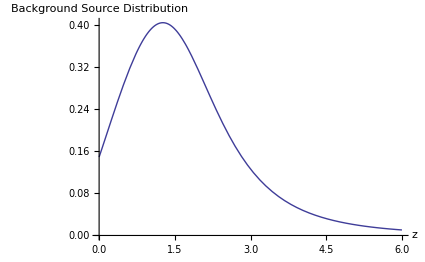

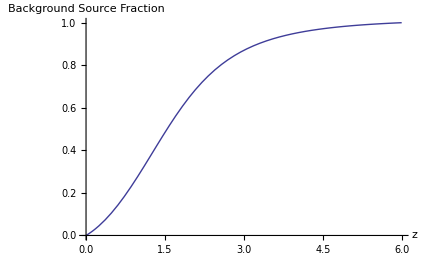

```mathematica
ΩM=0.3;
ΩΛ=0.7;
α=-1;
En[z_]:=√(ΩM(1+z)^3+ΩΛ)
Clear[Rv];
Rv[z_]:=0.015 (1+z)^2.7/(1+((1+z)/2.9)^5.6)
PDFz[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(NIntegrate[Rv[z]/((1+z)^(1/3)En[z]),{z,0,6}])^-1

Plot[PDFz[z],{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425]

Clear[P]
sol = P/.NDSolve[{P'[z]==PDFz[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[sol[z], {z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1}]
```

```mathematica
NIntegrate[Rv[z]/((1+z)^(1/3)En[z]),{z,0,6}]
```

0.100218

```mathematica
Rv[z]/((1+z)^(1/3)En[z])
```

(0.015 (1+z)^2.36667)/(√(0.7+0.3 (1+z)^3) (1+0.00257378 (1+z)^5.6))

```mathematica
PDFz[z]
```

(0.149674 (1+z)^2.36667)/(√(0.7+0.3 (1+z)^3) (1+0.00257378 (1+z)^5.6))